```mathematica
(*Задача 1*)
```

```mathematica
A={{1/2, 1/3, 1/2, 1}, {1/3, 1/2, 1, 1/2}, {1/2, 1, 1/2,1/3}, {1, 1/2, 1/3, 1/2}} 
Det[A]
MatrixForm[RowReduce[A]]
Eigenvectors[A]
```

{{1/2,1/3,1/2,1},{1/3,1/2,1,1/2},{1/2,1,1/2,1/3},{1,1/2,1/3,1/2}}

28/81

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

{{1,1,1,1},{-1,-1,1,1},{1,-1,-1,1},{-1,1,-1,1}}

```mathematica
(*Задача 2*)
Integrate[(Cos[x])^5 √Sin[x], x]
Clear[x]
```

2/231 Sin[x]^(3/2) (77-66 Sin[x]^2+21 Sin[x]^4)

```mathematica
(*Задача 3*)
h[x_] := x Sinh[x]
g[x_]:= D[h[y], {y, 100}]/.y->x
g[x] //Simplify
g[0] 
Clear[h, g, x]
```

100 Cosh[x]+x Sinh[x]

100

{{y[x]→-(√2)/(√(1+2 x+2 ⅇ^(2 x) C[1]))},{y[x]→(√2)/(√(1+2 x+2 ⅇ^(2 x) C[1]))}}

-(√2)/(√(1+2 ⅇ^(2 x)+2 x))

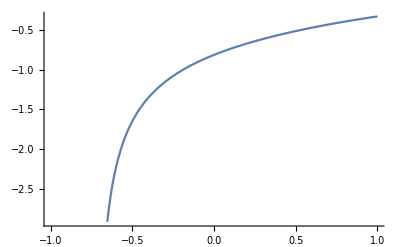

```mathematica
(*Задача 4*)
res = DSolve[y'[x]+y[x]== x*y[x]^3, y[x], x]

f[x_] = y[x]/.res⟦1⟧/.{C[1]-> 1}
Plot[f[x],{x, -1, 1}]
```

{{y[x]→InterpolatingFunction[…][x]}}

{InterpolatingFunction[…][x]}

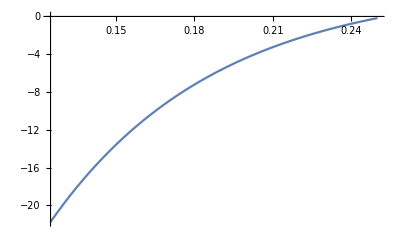

```mathematica
(*Задача 5*)
ress = NDSolve[{y''[x]+16y'[x] +2y[x] == 16/Sin[4x], y[π/8] ==3,y'[π/8]==2π},y[x],{x,1/8,1/4}]
t[x_] = y[x]/.ress
Plot[t[x], {x, 1/8,1/4}]
```